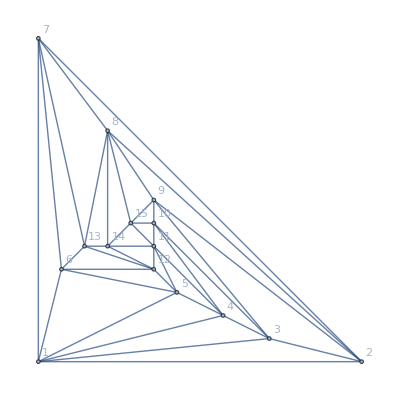

```mathematica
Graph[Graph[plantri[[3]]], VertexLabels->"Name",GraphLayout->"PlanarEmbedding"]
```

```mathematica
EmbedGraphInPlantri1[key_]:=Block[{val=allGraphs5[key], sets, reference={2,3,4,5,6}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[Graph[plantri[[1]]],1];
g=EdgeDelete[ g,{6<->2,2<->3,3<->4,4<->5,5<->6}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];
g
]
```

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri1[k],4],{k,alfa1s}]
```

{48,48,48,48,48}

```mathematica
With[
{graphs=Append[Append[Join[alfa1s,quads],K5Key],lambdaKey]},
Block[{forms=Monitor[Table[DeleteDuplicates[No5[FindFullFormulaN[EmbedGraphInPlantri1[kkk],4]]],{kkk,graphs}],ShowGraph5Least[kkk]], 
head=Table[With[{s=ShowGraph5Least[k]},If[k==29608,Framed[s],s]],{k,graphs}],
head2=Table[With[{s=Rotate[k,Pi/2]},If[k==29608,Framed[s],s]],{k,graphs}]},
Monitor[
TableForm[
Table[
Table[
With[{res=Length[Intersection[forms[[i]],forms[[j]]]]},If[i==j,Framed[res],res]]
,{i,Length[forms]}
]
,{j,Length[forms]}
],
TableHeadings->{head, head2}
],
{i,j}
]
]
]
```

| 36166 | 31738 | 29608 | 36112 | 31714 | 36085 | 29605 | 29527 | 31711 | 29551 | 29524 | 20665
-Graphics-361660 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 2
-Graphics-317380 | 0 | 2 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
-Graphics-296080 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-Graphics-361120 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
-Graphics-317140 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-Graphics-360850 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
-Graphics-296050 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
-Graphics-295270 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
-Graphics-317110 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2
-Graphics-295510 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
-Graphics-295240 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Graphics-206653 | 2 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 10